## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataA=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/4sem/431/tables/A.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataA//TableForm
```

a | b | c | d
551. | 2. | 27. | 0.343
542. | 3. | 18. | 0.343
537. | 4. | 13. | 0.337
534. | 5. | 10. | 0.33
532. | 6. | 8. | 0.324

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFit=data⟦2;;,{1,4}⟧;
fit=LinearModelFit[forFit,{1,x},x]
fit@"ParameterTable"
Plot[fit["Function"]@x, {x, 0, 32}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

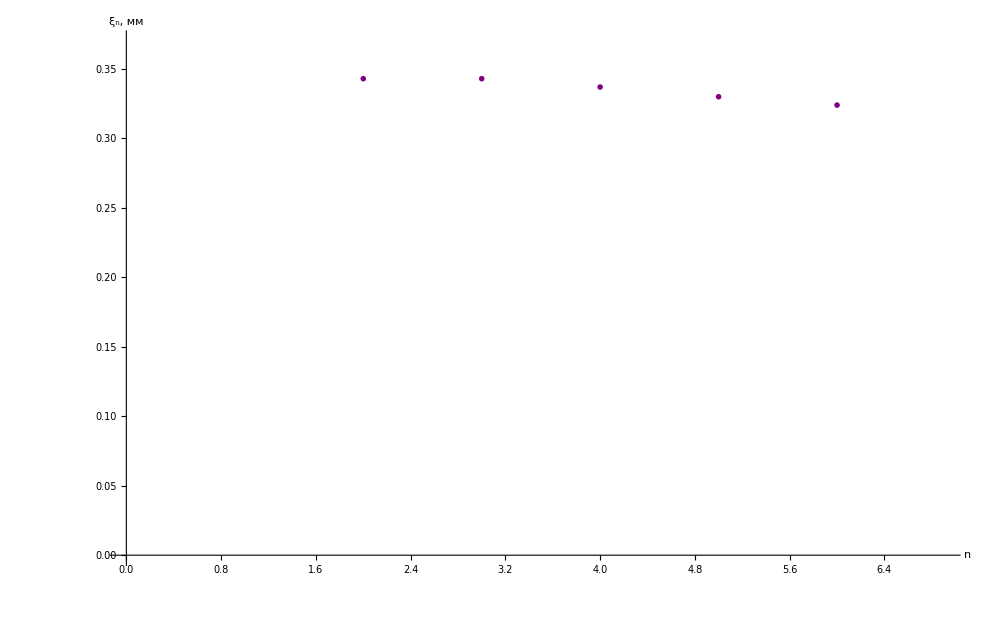

```mathematica
Show[ListPlot[dataA⟦2;;,{2,4}⟧,
GridLines->{grids@0.5,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"n","ξ_n, мм"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotMarkers->{"I", 50},
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,6.9},{0,0.37}}]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,6.9},{0,15}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXA=MapAt[dropLastDot@*ToString,dataA,{{2;;,All}}];
forTeXA//TeXForm
```

\left(
\begin{array}{cccc}
 \text{a} & \text{b} & \text{c} & \text{d} \\
 551 & 2 & 27 & 0.343 \\
 542 & 3 & 18 & 0.343 \\
 537 & 4 & 13 & 0.337 \\
 534 & 5 & 10 & 0.33 \\
 532 & 6 & 8 & 0.324 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
dataB=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/4sem/431/tables/B.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataB//TableForm
```

a |  | 
2.1 | 0.042 | 0.
2.35 | 0.047 | 1.
2.6 | 0.052 | 2.
2.85 | 0.057 | 3.
3.15 | 0.063 | 4.

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.0418+0.0052 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0418 | 0.000282843 | 147.785 | 6.83133×10^-7
x | 0.0052 | 0.00011547 | 45.0333 | 0.0000241045

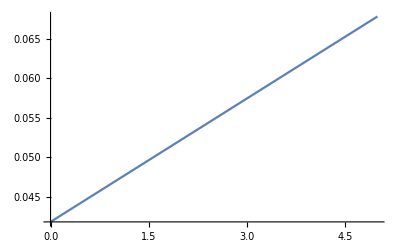

```mathematica
forFitB=dataB⟦2;;,{3,2}⟧;
fitB=LinearModelFit[forFitB,{1,x},x]
fitB@"ParameterTable"
Plot[fitB["Function"]@x, {x, 0, 5}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

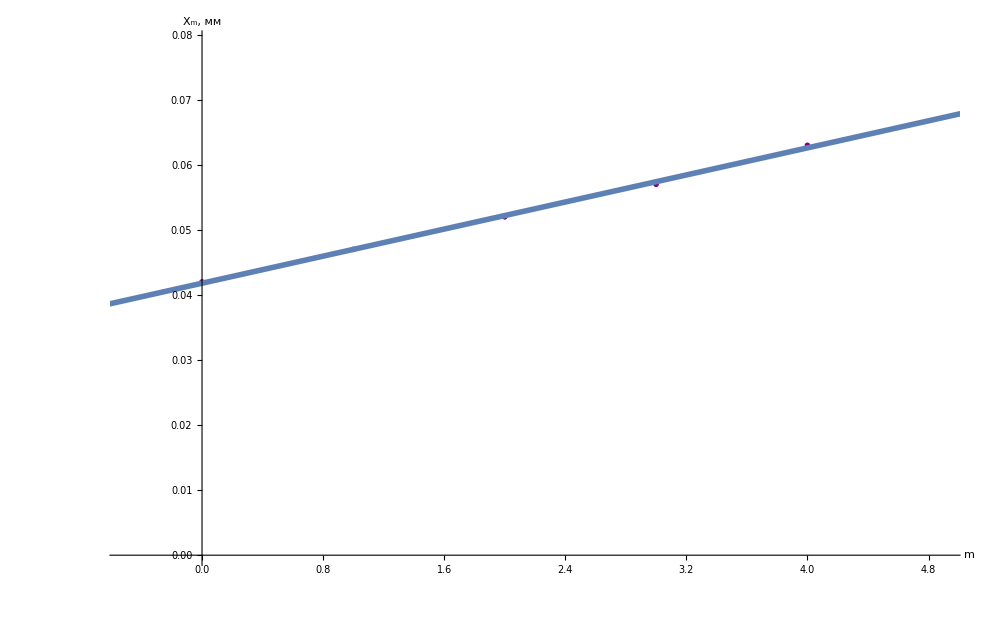

```mathematica
Show[ListPlot[dataB⟦2;;,{3,2}⟧,
GridLines->{grids@0.5,grids@0.005},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"m","X_m, мм"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotMarkers->{"I", 60},
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{-0.5,4.9},{0,0.079}}],
Plot[fitB["Function"]@x,{x,-1,6}, PlotStyle->Thickness@0.004]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,6.9},{0,15}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXB=MapAt[dropLastDot@*ToString,dataB,{{2;;,All}}];
forTeXB//TeXForm
```

\left(
\begin{array}{ccc}
 \text{a} & \text{} & \text{} \\
 2.1 & 0.042 & 0 \\
 2.35 & 0.047 & 1 \\
 2.6 & 0.052 & 2 \\
 2.85 & 0.057 & 3 \\
 3.15 & 0.063 & 4 \\
\end{array}
\right)